```mathematica
n = 10
DALL[p_,m_] = Sum[p^(i-1),{i,1,m}] 
LowerBound[p_,m_]=4*p(1-p)(m*p^(m-1))^2
LowerBound[p,n]
Plot[{DALL[p,n], LowerBound[p,n]},{p,0,1},PlotLegends->"Expressions"]
```

10

(-1+p^m)/(-1+p)

4 m^2 (1-p) p^(-1+2 m)

400 (1-p) p^19

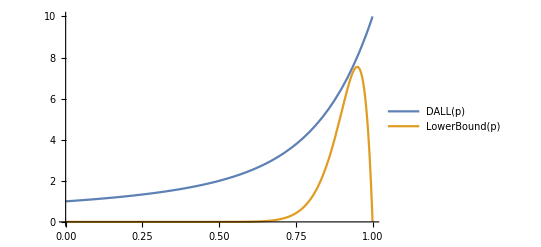

-Graphics-

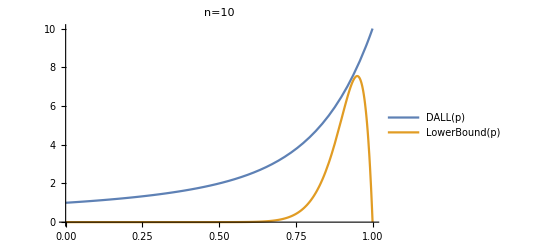

```mathematica
Show[%14,PlotLabel->HoldForm[n=10],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all10.eps",%15,"EPS"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all10.eps

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all.png",%54,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all.png

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all.png",%5,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all.png

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all.png",%402,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all.png

```mathematica
Export["/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all.png",%382,"PNG"]
```

/home/julia/git/ComplexityOfBooleanFunctions/plots/lowerbound_all.png

(p (-1+p^m))/(-1+p)

(p (-1+p^n))/(-1+p)

```mathematica
p->1
```

p→1

```mathematica
pr = p/.proot->1
```

p

```mathematica
pr
name = ToString[StringForm["tribes````", 1,2]]
filenameTemplate=StringTemplate["filename`n`.dat"];
filename=filenameTemplate[<|"n"->1234|>]
Directory[]
```

p

tribes12

filename1234.dat

/home/julia